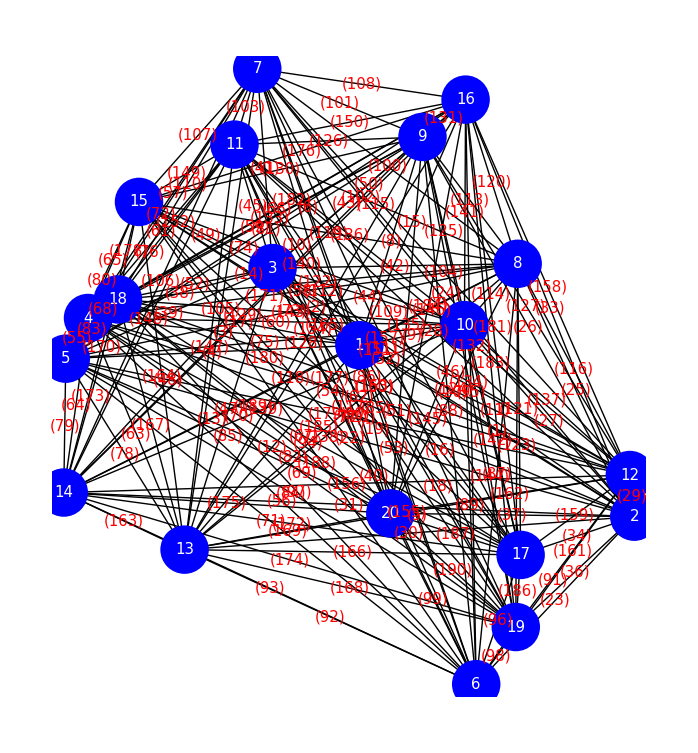

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{35.8668,{1,10,8,12,2,17,19,6,20,13,14,5,4,18,15,11,7,16,9,3,1}}

-Graphics-

```mathematica
PartLoopList1=PluralPartLoopByGreedyFromRank[PDCurrCostSort]
```

{{12→8,8→9,9→7,7→15,15→5,5→13,13→6,6→17,17→12},{12→8,8→9,9→7,7→15,15→5,5→13,13→6,6→19,19→12},{12→8,8→9,9→11,11→15,15→5,5→13,13→6,6→17,17→12},{12→8,8→9,9→11,11→15,15→5,5→13,13→6,6→19,19→12},{12→8,8→9,9→11,11→18,18→14,14→13,13→6,6→17,17→12},{12→8,8→9,9→11,11→18,18→14,14→13,13→6,6→19,19→12},{12→8,8→9,9→11,11→18,18→5,5→13,13→6,6→17,17→12},931,{2→12,12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→2},{2→12,12→8,8→16,16→9,9→7,7→11,11→15,15→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→7,7→11,11→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→7,7→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}}
 |  |  |  |

```mathematica
DelEdgePluralPartLoop[PartLoopList1]
```

{{12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,2→12}}

```mathematica
PartLoop1={12->8,8->16,16->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2,2->12}
```

{12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,2→12}

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

{2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,12,2}

-Graphics-